## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="PGMi";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data_model.csv";

mainFolder = "fit_PGMi";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGMi/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{3pg,Null,Keq substrate}

{0.189,Keq value}

{3pg,Km or S05 substrate}

{0.00021,Km or S05 value}

{2pg,Km or S05 substrate}

{0.000097,Km or S05 value}

{{{3pg,Null}},kcat substrates}

{22,kcat value}

{{{2pg,Null}},kcat substrates}

{10,kcat value}

((3pg)^c⇌(2pg)^c)^PGMi

;

Structure: 1

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg,Null | 0.189 | 0.17955
0.19845 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.00021 | 0.000171
0.000249 |  | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.000097 | 0.000083
0.000111 |  | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 22 | 21.
23. | 1/s | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null | 10 | 9.5
10.5 | 1/s | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
KeqList0[[1]][[3]]=0.98;
```

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((3pg)^c⇌(2pg)^c)^PGMi

;

Structure: 1

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg,Null | 0.98 | 0.17955
0.19845 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.00021 | 0.000171
0.000249 |  | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.000097 | 0.000083
0.000111 |  | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 22 | 21.
23. | 1/s | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null | 10 | 9.5
10.5 | 1/s | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGMi[c] + 3pg[c] <=> E_PGMi[c]&3pg",
				"E_PGMi[c]&3pg <=> E_PGMi[c]&2pg",
				"E_PGMi[c]&2pg <=> E_PGMi[c] + 2pg[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((PGMi^c)_^+(3pg)^c⇌(PGMi^c&(3pg)^c)_^)^PGMi1,((PGMi^c&(2pg)^c)_^⇌(PGMi^c)_^+(2pg)^c)^PGMi2,((PGMi^c&(3pg)^c)_^⇌(PGMi^c&(2pg)^c)_^)^PGMi3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModelOrig["Reactions"];
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{(3pg)^c→0}

{(2pg)^c→0}

{(3pg)^c→∞}

{(2pg)^c→∞}

Added inhibition reactions:

{}

Loading flux equation...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
PGMiRateConsts=finalRateConsts
Export[inputPath<>"/"<>rxnName<>"_rateConsts.m",PGMiRateConsts, "MX"]
```

{k_PGMi1^⟵,k_PGMi1^⟶,k_PGMi2^⟵,k_PGMi2^⟶,k_PGMi3^⟵,k_PGMi3^⟶}

/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGMi/fit_PGMi/input/PGMi_rateConsts.m

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	2pg[c]	3pg[c]	param_PGMi_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/haldaneRatio_1.txt"	0.98
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/haldaneRatio_1.txt"	0.98
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/haldaneRatio_1.txt"	0.98
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/haldaneRatio_1.txt"	0.98
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/haldaneRatio_1.txt"	0.98
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/haldaneRatio_1.txt"	0.98
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/haldaneRatio_1.txt"	0.98
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/haldaneRatio_1.txt"	0.98
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/haldaneRatio_1.txt"	0.98
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/haldaneRatio_1.txt"	0.98
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/haldaneRatio_1.txt"	0.98
1	0	0.000021000000000000012	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateFor_3pg.txt"	0.09090909090909095
1	0	0.000033282757041683415	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateFor_3pg.txt"	0.1368068886032101
1	0	0.000052749615061701256	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateFor_3pg.txt"	0.20076000891310197
1	0	0.0000836025058162344	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateFor_3pg.txt"	0.2847472489508014
1	0	0.00013250104234084062	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateFor_3pg.txt"	0.38686317984685703
1	0	0.00021000000000000012	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateFor_3pg.txt"	0.5000000000000001
1	0	0.00033282757041683416	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateFor_3pg.txt"	0.6131368201531433
1	0	0.0005274961506170126	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateFor_3pg.txt"	0.7152527510491988
1	0	0.0008360250581623448	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateFor_3pg.txt"	0.7992399910868984
1	0	0.0013250104234084062	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateFor_3pg.txt"	0.86319311139679
1	0	0.002100000000000001	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateFor_3pg.txt"	0.9090909090909091
1	9.700000000000007e-6	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateRev_2pg.txt"	0.09090909090909097
1	0.00001537346396687282	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateRev_2pg.txt"	0.13680688860321016
1	0.000024365298385642967	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateRev_2pg.txt"	0.200760008913102
1	0.00003861639554368923	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateRev_2pg.txt"	0.2847472489508014
1	0.00006120286241457877	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateRev_2pg.txt"	0.3868631798468571
1	0.00009700000000000008	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateRev_2pg.txt"	0.5000000000000002
1	0.00015373463966872819	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateRev_2pg.txt"	0.6131368201531432
1	0.00024365298385642967	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateRev_2pg.txt"	0.7152527510491988
1	0.0003861639554368927	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateRev_2pg.txt"	0.7992399910868985
1	0.0006120286241457877	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateRev_2pg.txt"	0.8631931113967901
1	0.0009700000000000008	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/relRateRev_2pg.txt"	0.9090909090909091
1	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateFor.txt"	22
1	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateFor.txt"	22
1	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateFor.txt"	22
1	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateFor.txt"	22
1	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateFor.txt"	22
1	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateFor.txt"	22
1	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateFor.txt"	22
1	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateFor.txt"	22
1	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateFor.txt"	22
1	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateFor.txt"	22
1	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateFor.txt"	22
1	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateRev.txt"	10
1	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateRev.txt"	10
1	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateRev.txt"	10
1	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateRev.txt"	10
1	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateRev.txt"	10
1	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateRev.txt"	10
1	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateRev.txt"	10
1	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateRev.txt"	10
1	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateRev.txt"	10
1	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateRev.txt"	10
1	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_i/fit_PGMi/input/absRateRev.txt"	10

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«18 more identical outputs»

```mathematica
FilePrint[dataPathList[[18]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.13680688860321014
0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310194
0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.28474724895080133
0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.386863179846857
0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000002
0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491989
0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909093
0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.090909090909091
0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.1368068886032102
0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131019
0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508017
0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.3868631798468571
0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.5000000000000003
0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.6131368201531434
0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491988
0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868984
0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.86319311139679
0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909092
0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.09090909090909094
0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321008
0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310175
0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508015
0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468569
0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491988
0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.8631931113967899
0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909092
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=50;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 0.503490420333
best_fit: 1.05484093138
best_fit: 0.864868901407
best_fit: 1.08569953859
best_fit: 0.763563234483
best_fit: 0.674110254756
best_fit: 0.572027179216
best_fit: 1.08190674538
best_fit: 0.826344091199
best_fit: 1.09635854047
best_fit: 0.85735938233
best_fit: 1.09639755292
best_fit: 0.875126629227
best_fit: 0.494414702354
best_fit: 1.09449105919
best_fit: 5.90066974617
best_fit: 0.96528112742
best_fit: 0.619886339324
best_fit: 0.900997774193
best_fit: 0.996764059484
best_fit: 0.848689269354
best_fit: 0.822076338492
best_fit: 1.08135951216
best_fit: 1.08955265983
best_fit: 1.08908949993
best_fit: 1.09191334212
best_fit: 1.06711992182
best_fit: 1.01038715633
best_fit: 0.969215586625
best_fit: 0.445663249035
best_fit: 0.280838837302
best_fit: 1.01558482506
best_fit: 0.686946842062
best_fit: 0.801163774977
best_fit: 1.09839939125
best_fit: 0.896148041149
best_fit: 1.02870244843
best_fit: 0.845133307395
best_fit: 1.08225762991
best_fit: 0.339570305523
best_fit: 1.08561206792
best_fit: 0.626023713744
best_fit: 1.02609671021
best_fit: 1.0951492313
best_fit: 0.948279056779
best_fit: 1.0914662162
best_fit: 0.952332312944
best_fit: 1.08953107216
best_fit: 0.878908454639
best_fit: 0.520648570337

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.000346078 | 1.1977×10^-7 | 0.000781247 | 0.0797191 | 0.98 | 0.980781
1 | haldaneRatio_1 | 0.000346078 | 1.1977×10^-7 | 0.000781247 | 0.0797191 | 0.98 | 0.980781
1 | haldaneRatio_1 | 0.000346078 | 1.1977×10^-7 | 0.000781247 | 0.0797191 | 0.98 | 0.980781
1 | haldaneRatio_1 | 0.000346078 | 1.1977×10^-7 | 0.000781247 | 0.0797191 | 0.98 | 0.980781
1 | haldaneRatio_1 | 0.000346078 | 1.1977×10^-7 | 0.000781247 | 0.0797191 | 0.98 | 0.980781
1 | haldaneRatio_1 | 0.000346078 | 1.1977×10^-7 | 0.000781247 | 0.0797191 | 0.98 | 0.980781
1 | haldaneRatio_1 | 0.000346078 | 1.1977×10^-7 | 0.000781247 | 0.0797191 | 0.98 | 0.980781
1 | haldaneRatio_1 | 0.000346078 | 1.1977×10^-7 | 0.000781247 | 0.0797191 | 0.98 | 0.980781
1 | haldaneRatio_1 | 0.000346078 | 1.1977×10^-7 | 0.000781247 | 0.0797191 | 0.98 | 0.980781
1 | haldaneRatio_1 | 0.000346078 | 1.1977×10^-7 | 0.000781247 | 0.0797191 | 0.98 | 0.980781
1 | haldaneRatio_1 | 0.000346078 | 1.1977×10^-7 | 0.000781247 | 0.0797191 | 0.98 | 0.980781
1 | relRateFor_3pg | 0.00929271 | 0.0000863544 | 0.00192454 | 2.11699 | 0.0909091 | 0.0889846
1 | relRateFor_3pg | 0.00882827 | 0.0000779384 | 0.00275292 | 2.01226 | 0.136807 | 0.134054
1 | relRateFor_3pg | 0.00818032 | 0.0000669176 | 0.0037461 | 1.86596 | 0.20076 | 0.197014
1 | relRateFor_3pg | 0.00732791 | 0.0000536982 | 0.00476427 | 1.67316 | 0.284747 | 0.279983
1 | relRateFor_3pg | 0.00628924 | 0.0000395546 | 0.005562 | 1.43772 | 0.386863 | 0.381301
1 | relRateFor_3pg | 0.00513558 | 0.0000263741 | 0.00587773 | 1.17555 | 0.5 | 0.494122
1 | relRateFor_3pg | 0.00397884 | 0.0000158311 | 0.00559166 | 0.911977 | 0.613137 | 0.607545
1 | relRateFor_3pg | 0.00293212 | 8.59734×10^-6 | 0.00481274 | 0.672872 | 0.715253 | 0.71044
1 | relRateFor_3pg | 0.00206934 | 4.28216×10^-6 | 0.00379918 | 0.475349 | 0.79924 | 0.795441
1 | relRateFor_3pg | 0.00141121 | 1.99151×10^-6 | 0.00280033 | 0.324416 | 0.863193 | 0.860393
1 | relRateFor_3pg | 0.000938269 | 8.8035×10^-7 | 0.00196192 | 0.215811 | 0.909091 | 0.907129
1 | relRateRev_2pg | 0.00938229 | 0.0000880273 | 0.00198532 | 2.18386 | 0.0909091 | 0.0928944
1 | relRateRev_2pg | 0.00890371 | 0.000079276 | 0.0028337 | 2.07131 | 0.136807 | 0.139641
1 | relRateRev_2pg | 0.00823774 | 0.0000678604 | 0.00384438 | 1.91491 | 0.20076 | 0.204604
1 | relRateRev_2pg | 0.00736471 | 0.0000542389 | 0.00486988 | 1.71025 | 0.284747 | 0.289617
1 | relRateRev_2pg | 0.00630558 | 0.0000397604 | 0.00565789 | 1.46251 | 0.386863 | 0.392521
1 | relRateRev_2pg | 0.00513516 | 0.0000263698 | 0.00594716 | 1.18943 | 0.5 | 0.505947
1 | relRateRev_2pg | 0.00396788 | 0.0000157441 | 0.00562752 | 0.917825 | 0.613137 | 0.618764
1 | relRateRev_2pg | 0.002917 | 8.50887×10^-6 | 0.00482026 | 0.673924 | 0.715253 | 0.720073
1 | relRateRev_2pg | 0.00205458 | 4.2213×10^-6 | 0.00379004 | 0.474205 | 0.79924 | 0.80303
1 | relRateRev_2pg | 0.00139903 | 1.95728×10^-6 | 0.00278516 | 0.322657 | 0.863193 | 0.865978
1 | relRateRev_2pg | 0.00092916 | 8.63339×10^-7 | 0.00194706 | 0.214176 | 0.909091 | 0.911038
1 | absRateFor | 6.88579×10^-7 | 4.74142×10^-13 | 0.0000348812 | 0.000158551 | 22 | 22.
1 | absRateFor | 6.88579×10^-7 | 4.74142×10^-13 | 0.0000348812 | 0.000158551 | 22 | 22.
1 | absRateFor | 6.88579×10^-7 | 4.74142×10^-13 | 0.0000348812 | 0.000158551 | 22 | 22.
1 | absRateFor | 6.88579×10^-7 | 4.74142×10^-13 | 0.0000348812 | 0.000158551 | 22 | 22.
1 | absRateFor | 6.88579×10^-7 | 4.74142×10^-13 | 0.0000348812 | 0.000158551 | 22 | 22.
1 | absRateFor | 6.88579×10^-7 | 4.74142×10^-13 | 0.0000348812 | 0.000158551 | 22 | 22.
1 | absRateFor | 6.88579×10^-7 | 4.74142×10^-13 | 0.0000348812 | 0.000158551 | 22 | 22.
1 | absRateFor | 6.88579×10^-7 | 4.74142×10^-13 | 0.0000348812 | 0.000158551 | 22 | 22.
1 | absRateFor | 6.88579×10^-7 | 4.74142×10^-13 | 0.0000348812 | 0.000158551 | 22 | 22.
1 | absRateFor | 6.88579×10^-7 | 4.74142×10^-13 | 0.0000348812 | 0.000158551 | 22 | 22.
1 | absRateFor | 6.88579×10^-7 | 4.74142×10^-13 | 0.0000348812 | 0.000158551 | 22 | 22.
1 | absRateRev | 3.32448×10^-6 | 1.10522×10^-11 | 0.0000765493 | 0.000765493 | 10 | 10.0001
1 | absRateRev | 3.32448×10^-6 | 1.10522×10^-11 | 0.0000765493 | 0.000765493 | 10 | 10.0001
1 | absRateRev | 3.32448×10^-6 | 1.10522×10^-11 | 0.0000765493 | 0.000765493 | 10 | 10.0001
1 | absRateRev | 3.32448×10^-6 | 1.10522×10^-11 | 0.0000765493 | 0.000765493 | 10 | 10.0001
1 | absRateRev | 3.32448×10^-6 | 1.10522×10^-11 | 0.0000765493 | 0.000765493 | 10 | 10.0001
1 | absRateRev | 3.32448×10^-6 | 1.10522×10^-11 | 0.0000765493 | 0.000765493 | 10 | 10.0001
1 | absRateRev | 3.32448×10^-6 | 1.10522×10^-11 | 0.0000765493 | 0.000765493 | 10 | 10.0001
1 | absRateRev | 3.32448×10^-6 | 1.10522×10^-11 | 0.0000765493 | 0.000765493 | 10 | 10.0001
1 | absRateRev | 3.32448×10^-6 | 1.10522×10^-11 | 0.0000765493 | 0.000765493 | 10 | 10.0001
1 | absRateRev | 3.32448×10^-6 | 1.10522×10^-11 | 0.0000765493 | 0.000765493 | 10 | 10.0001
1 | absRateRev | 3.32448×10^-6 | 1.10522×10^-11 | 0.0000765493 | 0.000765493 | 10 | 10.0001

### Simulated Data and Best Fit Data Plot

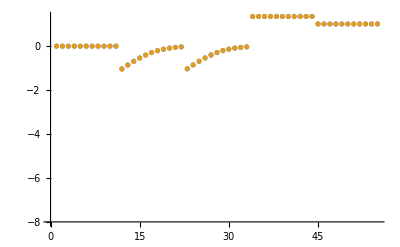

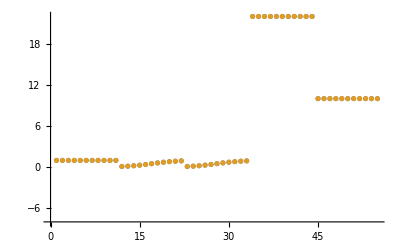

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

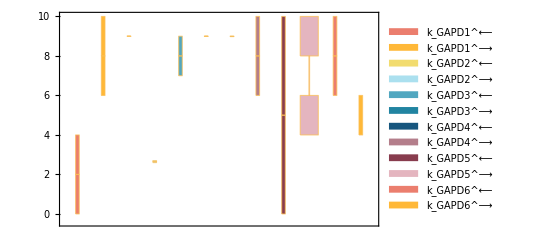

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

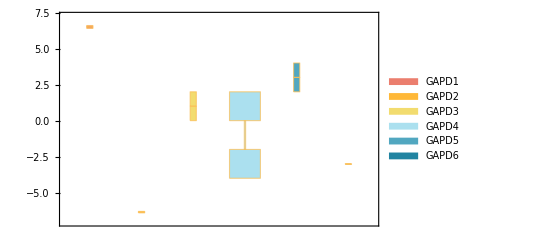

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

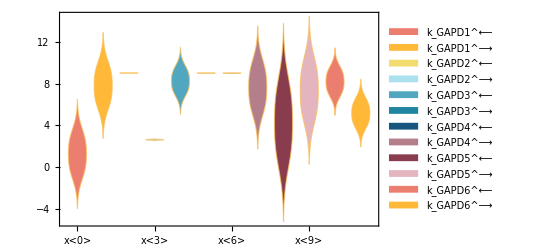

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

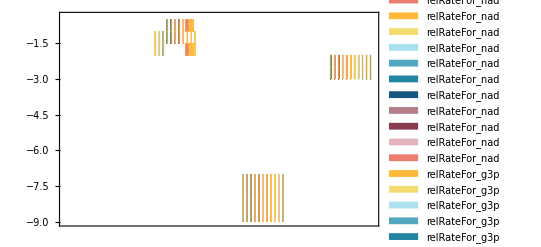

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.00021 | 0.000253218 | 20.58
0.000097 | 0.0000801921 | 17.3277

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
22 | 21.9997 | 0.0012649
10 | 10.0006 | 0.00611159

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.7 | 0.70863 | 1.23279